## Initialize notebook

```mathematica
Quit[];
```

```mathematica
<<Toolbox`
<<Toolbox`Style`
<<MASSef`

baseDir = "/home/mrama/Dropbox/PhD_stuff/Projects/eMASS/";
```

```mathematica
outputDir=baseDir <>"old_model_building_flux/whole_model_output/";
Import[baseDir<>"old_model_building_flux/functions.m"];
```

```mathematica
allEnzymes = {"ENO", "FBA1", "FBA2",  "GAPD", "PGK", "PGMd", "PGMi", "TPI"};
```

## Build models

#### Import all enzyme models

```mathematica
allModels = 
Table[
Import[baseDir<>"old_model_building_flux"<>enzName<>"/model_"<> enzName <>".mx", "MX"],
{enzName, allEnzymes}];
```

```mathematica
MapThread[#1-> #2&,{allEnzymes,Map[Length@#&,allModels]}]
```

{ENO→50,FBA1→20,FBA2→15,GAPD→50,PGK→36,PGMd→37,PGMi→49,TPI→48}

#### Build model combinations

```mathematica
rateConstSetList=Tuples[Range[3],{8}];
Length@rateConstSetList
```

6561

```mathematica
i=0;
modelList=Table[

Print[i];
i=i+1;

modelSubList =Table[
	allModels[[i]][[rateConstSet[[i]]]],
{i, 1, Length@rateConstSet}];

Union@@modelSubList,

{rateConstSet, rateConstSetList}];
```

```mathematica
Export[outputDir<>"model_8enz_top3.mx",modelList,"MX"];
```

#### Get met_free fractions

```mathematica
freeMetFraction=Table[
Values@getFreeMetFraction[modelList[[modelI]]],
{modelI, 1, Length@modelList}];

header =Map[getID[#]&, Keys@getFreeMetFraction[modelList[[1]]]];
freeMetFraction=Join[{header}, freeMetFraction];

Export[outputDir<>"free_met_fraction.csv", freeMetFraction, "CSV"];
```

#### Get enz_form fractions

```mathematica
enzFormFraction=Table[
Values@getEnzFormFraction[modelList[[modelI]]],
{modelI, 1, Length@modelList}];

header=Keys@getEnzFormFraction[modelList[[1]]];
enzNames = Map[getID@#&,header]
boundMets = Map[getCatalytic[#]&,header];
header=Table[
StringRiffle[Flatten@{enzNames[[i]],Map[getID@#&,boundMets[[i]]]}, "_"],
{i, 1, Length@boundMets}];

enzFormFraction=Join[{header}, enzFormFraction];
Export[outputDir<>"enz_form_fraction.csv", enzFormFraction, "CSV"];
```

{ENO,ENO,ENO,FBA1,FBA1,FBA1,FBA1,FBA2,FBA2,FBA2,FBA2,FBA2,FBA2,GAPD,GAPD,GAPD,GAPD,GAPD,GAPD,PGK,PGK,PGK,PGK,PGK,PGK,PGK,PGMd,PGMd,PGMd,PGMd,PGMi,PGMi,PGMi,TPI,TPI,TPI}

#### Get rates

```mathematica
elemRates=Table[
Values@getElemRates[modelList[[modelI]]],
{modelI, 1, Length@modelList}];
```

```mathematica
header=Keys@getElemRates[modelList[[1]]];
header=Map[getID[#]&,header];

header=Table[

If[OddQ[i],
"k^r_"<>header[[i]],
"k^f_"<>header[[i]]],

{i,1,Length@header}];


elemRates=Join[{header}, elemRates];
Export[outputDir<>"rates.csv", elemRates, "CSV"];
```

#### Get met_free fractions - only same models as in eMASS2

```mathematica
goodModelsInd=Import[baseDir<>"eMASSpy/data_8enz/good_models_ind_list.m",  "MX"];
```

```mathematica
freeMetFraction=Table[
Values@getFreeMetFraction[modelList[[modelI+1]]],
{modelI, goodModelsInd}];

header =Map[getID[#]&, Keys@getFreeMetFraction[modelList[[1]]]];
freeMetFraction=Join[{header}, freeMetFraction];

Export[outputDir<>"free_met_fraction_models_newVol.csv", freeMetFraction, "CSV"];
```

#### Get enz_form fractions - only same models as in eMASS2

```mathematica
enzFormFraction=Table[
Values@getEnzFormFraction[modelList[[modelI+1]]],
{modelI, goodModelsInd}];

header=Keys@getEnzFormFraction[modelList[[1]]];
enzNames = Map[getID@#&,header];
boundMets = Map[getCatalytic[#]&,header];
header=Table[
StringRiffle[Flatten@{enzNames[[i]],Map[getID@#&,boundMets[[i]]]}, "_"],
{i, 1, Length@boundMets}];

enzFormFraction=Join[{header}, enzFormFraction];
Export[outputDir<>"enz_form_fraction_models_newVol.csv", enzFormFraction, "CSV"];
```

#### Import models

```mathematica
modelList = Import[outputDir<>"model_8enz_top3.mx","MX"];
```

```mathematica
Length@modelList
```

6561

#### Update met_free concentrations

```mathematica
updatedModelList = 
Table[
	updateFreeMetConc[model],
{model, modelList}];
```

```mathematica
Export[outputDir<>"model_8enz_top3_free_mets.mx",updatedModelList,"MX"];
```

#### Import models with updated free metabolite concentrations

```mathematica
updatedModelList= Import[outputDir<>"model_8enz_top3_free_mets.mx","MX"];
```

#### Import updated models

```mathematica
goodModelsInd=Import[baseDir<>"eMASSpy/data_8enz/good_models_ind_list.m",  "MX"];
```

#### Define model subsets based on initial ATP concentration

```mathematica
atpBelow007Subset=Import[baseDir<>"eMASSpy/data_8enz/atpBelow007_subset.m",  "MX"];
atpAbove0095Subset=Import[baseDir<>"eMASSpy/data_8enz/atpAbove0095_subset.m",  "MX"];
atpBetweenSubset=Import[baseDir<>"eMASSpy/data_8enz/atpBetween_subset.m",  "MX"];
```

```mathematica
Select[Flatten@stripUnits@Values@Map[FilterRules[#["InitialConditions"], atp^c]&,updatedModelList[[goodModelsInd+1]][[atpAbove0095Subset]]], #<0.0095&]
```

{}

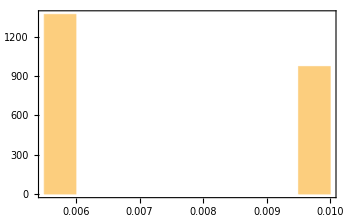

```mathematica
Histogram[Flatten@Values@stripUnits@Map[FilterRules[#["InitialConditions"], atp^c]&,updatedModelList[[goodModelsInd]]]]
```

#### Check which models cannot be simulated

```mathematica
simRes=Table[
	CheckAbort[simulate[updatedModelList[[i]], {t, 0,10}],{}],
{i,1,Length@updatedModelList}];
```

## Model simulation

#### simulate model

```mathematica
metList=Cases[updatedModelList[[1]]["Species"], _metabolite,Infinity]
```

{(13dpg)^c,(2pg)^c,(3pg)^c,adp^c,atp^c,dhap^c,fdp^c,g3p^c,nad^c,nadh^c,pep^c,pi^c,(23dpg)^c}

```mathematica
simulateResAtpBelow007 = Table[
simulate[updatedModelList[[goodModelsInd+1]][[entryI]], {t,0,500}],
{entryI, atpBelow007Subset}];
```

```mathematica
simulateResAtpAbove0095 = Table[
simulate[updatedModelList[[goodModelsInd+1]][[entryI]], {t,0,500}],

{entryI,atpAbove0095Subset}];
```

#### Plot simulation results

```mathematica
concPlotListAtpBelow007 =Table[
plotSimulation[FilterRules[simulateResAtpBelow007[[i,1]], metList], PlotFunction->LogPlot],
{i, 1, Length@atpBelow007Subset}];
```

```mathematica
concPlotListAtpAbove0095 =Table[
plotSimulation[FilterRules[simulateResAtpAbove0095[[i,1]], metList], PlotFunction->LogPlot],
{i, 1, Length@atpAbove0095Subset}];
```

```mathematica
Show[concPlotListAtpBelow007, PlotRange-> {{0,100},Automatic}]
```

-Graphics-

```mathematica
Show[concPlotListAtpAbove0095, PlotRange-> {{0,100},Automatic}]
```

-Graphics-

#### Save simulation results

```mathematica
Import[baseDir"code/simulation.m"];
```

```mathematica
indEnz=Map[Position[Keys@simulateResAtpBelow007[[2,1]],#]&,Cases[modelList[[1]]["Species"],_enzyme, Infinity]]//Flatten;
 indMet=Map[Position[Keys@simulateResAtpBelow007[[2,1]],#]&,Cases[modelList[[1]]["Species"],_metabolite, Infinity]]//Flatten;
```

```mathematica
headerConcEnz=Keys@simulateResAtpBelow007[[2,1]][[indEnz]];
enzNames = Map[getID@#&,headerConcEnz];
boundMets = Map[getCatalytic[#]&,headerConcEnz];
headerConcEnz=Table[
StringRiffle[Flatten@{enzNames[[i]],Map[getID@#&,boundMets[[i]]]}, "_"],
{i, 1, Length@boundMets}];
```

```mathematica
headerConcMets=Map[getID@#&,Keys@simulateResAtpBelow007[[2,1]][[indMet]]];
```

```mathematica
headerFlux=Map[getID[#]&,Keys@simulateResAtpBelow007[[2,2]]];
```

```mathematica
tValues=Map[10^#&,Range[-6,2, 0.1]];
tFinal=500;
tValues=Insert[tValues,0., 1];
```

```mathematica
modelID="simulateResAtpBelow007";
getSimulationData[simulateResAtpBelow007, outputDir,  modelID, tFinal, tValues, 
				 headerConcEnz, headerConcMets, headerFlux, indEnz, indMet];
```

```mathematica
modelID="simulateResAtpAbove0095";
getSimulationData[simulateResAtpAbove0095, outputDir,  modelID, tFinal, tValues, 
				 headerConcEnz, headerConcMets, headerFlux, indEnz, indMet];
```

## Model analysis

```mathematica
eigenvaluesList = Table[

jacobian=getJacobian[updatedModelList[[ind]]]/.stripUnits[updatedModelList[[ind]]["InitialConditions"]]/.stripUnits[updatedModelList[[ind]]["Parameters"]];
Eigenvalues[jacobian],

{ind, 1, Length@updatedModelList}];
```

```mathematica
Export[outputDir<> "eigenvalues_list.csv", eigenvaluesList, "CSV"];
```

```mathematica
eigenvaluesList[[goodModelsInd]]//Length
```

2341

```mathematica
Export[outputDir<> "eigenvalues_list_models_newVol.csv", eigenvaluesList[[goodModelsInd+1]], "CSV"];
```

```mathematica
stableModelsIndListNoIM= Flatten@Position[Map[AllTrue[#, Internal`RealValuedNumericQ]&,eigenvaluesList[[goodModelsInd+1]]], True]
```

```mathematica
eigenvaluesMax = Map[{Max@#[[1]],Max@#[[2]]}&,Map[{Re[#], Im[#]}&,eigenvaluesList[[goodModelsInd+1]]]];
```

```mathematica
Export[outputDir<>"eigenvalues_max.csv", eigenvaluesMax, "CSV"];
Export[outputDir<>"eigenvalues_max_re.csv", eigenvaluesMax[[All,1]], "CSV"];
Export[outputDir<>"eigenvalues_max_im.csv", eigenvaluesMax[[All,2]], "CSV"];
```

```mathematica
Export[outputDir<>"eigenvalues_max_mod_models_newVol.csv", eigenvaluesMax, "CSV"];
Export[outputDir<>"eigenvalues_max_re_models_newVol.csv", eigenvaluesMax[[All,1]], "CSV"];
Export[outputDir<>"eigenvalues_max_im_models_newVol.csv", eigenvaluesMax[[All,2]], "CSV"];
```

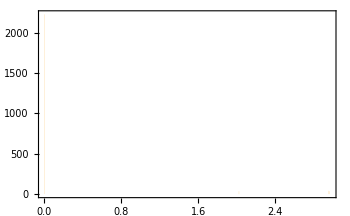

```mathematica
Histogram[eigenvaluesMax[[All,1]]]
```

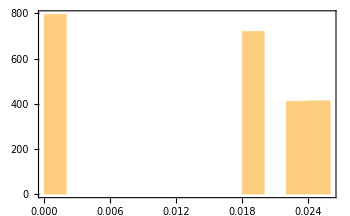

```mathematica
Histogram[eigenvaluesMax[[All,2]]]
```